# Star

### 先准备好2D曲线

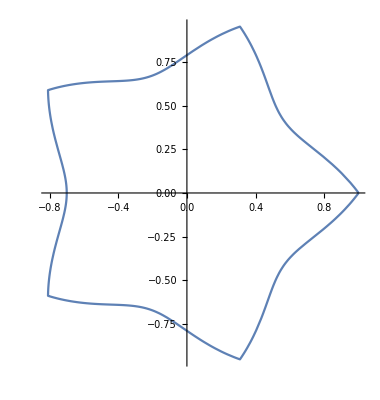

```mathematica
ParametricPlot[{Cos[θ],Sin[θ]}(1-0.3Abs@Sin[5/2θ]),{θ,0,2π}]
```

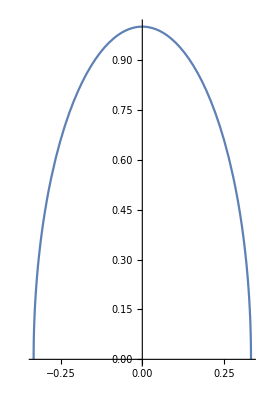

```mathematica
ParametricPlot[{d/3,√(1-d^2)},{d,-1,1}]
```

```mathematica
Manipulate[ParametricPlot3D[{Cos[θ]r,d/3,Sin[θ]r}/.r->√(1-d^2)(1-0.3Abs@Sin[n/2θ]),{θ,0,2π},{d,-1,1},PlotPoints->50],{n,5,10,1}]
```

#### 太丑了

换一个侧面曲线

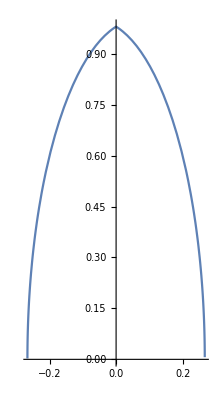

```mathematica
ParametricPlot[{d/3,√(1-(Abs@d+0.2)^2)},{d,-1,1}]
```

```mathematica
Manipulate[ParametricPlot3D[{Cos[θ]r,d/3,Sin[θ]r}/.r->√(1-(Abs@d+0.2)^2)(1-a Abs@Sin[n/2θ]),{θ,0,2π},{d,-1,1},PlotPoints->50],{{n,5},3,10,1},{{a,0.4},0.1,0.9}]
```